```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/quantum_stochastic/math

### QW inflection

```mathematica
Integrate[Sin[(3π)/2 x]^2,{x,0,1}]
```

1/2

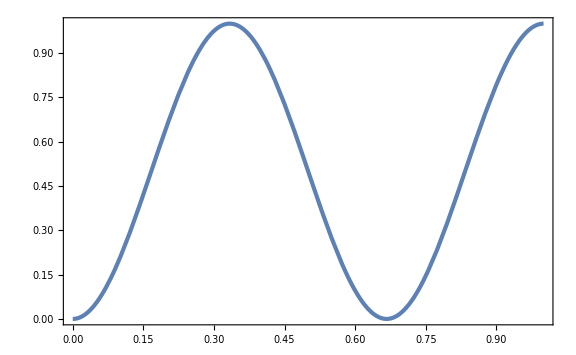

```mathematica
Plot[Sin[(1+1/2)π x]^2,{x,0,1}]
```

```mathematica
normN=Integrate[Exp[(-(x-1)^2)/σ^2],{x,0,1}]^(-1/2)
```

(√2)/(π^(1/4) √(σ Erf[1/σ]))

```mathematica
Integrate[(normN Exp[(-(x-1)^2)/(2 σ^2)])^2,{x,0,1}]
```

1

```mathematica
αn[n_]= Integrate[normN Exp[(-(x-1)^2)/(2 σ^2)]Sqrt[2]Sin[(n+1/2)π x],{x,0,1}]//Simplify
```

-(ⅈ ⅇ^(-1/8 π (8 ⅈ n+π (σ+2 n σ)^2)) π^(1/4) σ ((-1+ⅇ^(2 ⅈ n π)) Erfi[((1+2 n) π σ)/(2 √2)]-ⅇ^(2 ⅈ n π) Erfi[(-2 ⅈ+(1+2 n) π σ^2)/(2 √2 σ)]+Erfi[(2 ⅈ+(1+2 n) π σ^2)/(2 √2 σ)]))/(√2 √(σ Erf[1/σ]))

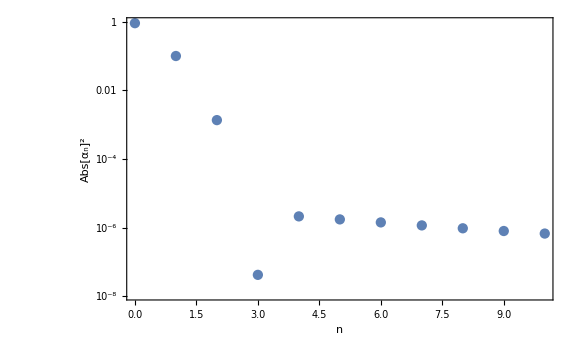

```mathematica
ListLogPlot[Table[{n,Abs[N[αn[n]/.{σ->1/3},30]]^2},{n,0,10}],Joined->False,FrameLabel->{n,Abs[Subscript[α, n]]^2}]
```

### QW hilltop

```mathematica
Integrate[Sin[2π x]^2,{x,0,1}]
```

1/2

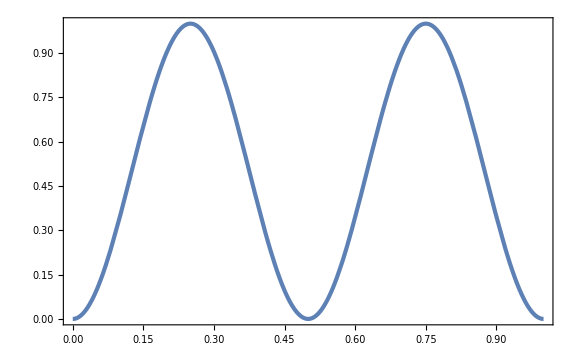

```mathematica
Plot[Sin[2π x]^2,{x,0,1}]
```

```mathematica
Integrate[Exp[(-(x-1/2)^2)/σ^2],{x,0,1}]
```

√π σ Erf[1/(2 σ)]

```mathematica
normN=Integrate[Exp[(-(x-1/2)^2)/σ^2],{x,0,1}]^(-1/2)
```

1/(π^(1/4) √(σ Erf[1/(2 σ)]))

```mathematica
Integrate[(normN Exp[(-(x-1/2)^2)/(2 σ^2)])^2,{x,0,1}]
```

1

```mathematica
αn[n_]= Integrate[normN Exp[(-(x-1/2)^2)/(2 σ^2)]Sqrt[2]Sin[n π x],{x,0,1}]//Simplify
```

(ⅇ^(-1/2 n π (ⅈ+n π σ^2)) (-1+ⅇ^(ⅈ n π)) π^(1/4) σ (Erfi[(-ⅈ+2 n π σ^2)/(2 √2 σ)]-Erfi[(ⅈ+2 n π σ^2)/(2 √2 σ)]))/(2 √(σ Erf[1/(2 σ)]))

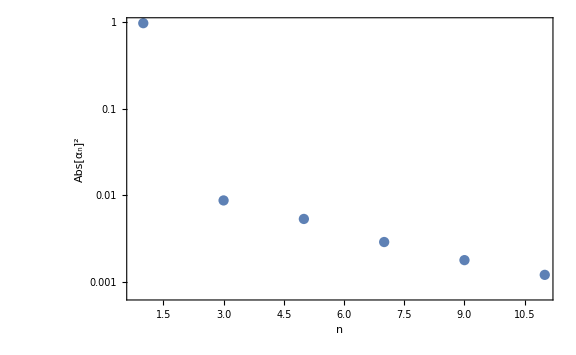

```mathematica
ListLogPlot[Table[{n,Abs[N[αn[n]/.{σ->1/3},30]]^2},{n,1,11}],Joined->False,FrameLabel->{n,Abs[Subscript[α, n]]^2},PlotRange->Full]
```

### hilltop

```mathematica
w[x_]=E^(1/v[x])/v[x];
LFPF=Collect[w[x]^(1/2)((-v'[x])/v[x] D[(w[x]^(-1/2)F[x]), x]+v[x]D[D[(w[x]^(-1/2)F[x]), x], x])//Simplify,{F[x],F'[x],F''[x]},Simplify]
```

F'[x] v'[x]+v[x] F''[x]+(F[x] (-((1+4 v[x]+v[x]^2) v'[x]^2)+2 v[x]^2 (1+v[x]) v''[x]))/(4 v[x]^3)

```mathematica
Collect[w[x]^(-1/2)(D[(v'[x]/v[x] w[x]^(1/2)F[x]), x]+D[D[(v[x] w[x]^(1/2)F[x]), x], x])//Simplify,{F[x],F'[x],F''[x]},Simplify]
```

F'[x] v'[x]+v[x] F''[x]+(F[x] (-((1+4 v[x]+v[x]^2) v'[x]^2)+2 v[x]^2 (1+v[x]) v''[x]))/(4 v[x]^3)

```mathematica
(D[(v'[x]/v[x] w[x]F[x]), x]+D[D[(v[x]w[x]F[x]), x], x])/w[x]//Simplify
```

-(F'[x] v'[x])/v[x]+v[x] F''[x]

```mathematica
vh[x_]=v0(1-(x/M)^p)^2;
```

```mathematica
DSolve[Simplify[Normal[Series[Simplify[(-v'[x])/v[x] F'[x]+v[x] F''[x]==-Λn F[x]/.{v[x]->v0,v'[x]->vh'[ϵ^(1/p) M],v''[x]->vh''[ϵ^(1/p) M]},{ϵ>0,p>0}],{ϵ,0,1}]]/.{ϵ->(x/M)^p},{p>0,x>0,M>0}]/.{p->4},F[x],x]
```

{{F[x]→[x]}}

```mathematica
Simplify[Normal[Series[Simplify[LFPF/.{v[x]->v0,v'[x]->vh'[ϵ^(1/p) M],v''[x]->vh''[ϵ^(1/p) M]},{ϵ>0,p>0}],{ϵ,0,1}]]/.{ϵ->(x/M)^p},{p>0,x>0,M>0}]
```

(-((-1+p) p (1+v0) (x/M)^p F[x])+v0 x (-2 p (x/M)^p F'[x]+x F''[x]))/x^2

```mathematica
Simplify[Normal[Series[Simplify[(-((1+4 v[x]+v[x]^2) v'[x]^2)+2 v[x]^2 (1+v[x]) v''[x])/(4 v[x]^3)/.{v[x]->vh[ϵ^(1/p) M],v'[x]->vh'[ϵ^(1/p) M],v''[x]->vh''[ϵ^(1/p) M]},{ϵ>0,p>0}],{ϵ,0,1}]]/.{ϵ->(x/M)^p},{p>0,x>0,M>0}]
```

-((-1+p) p (1+v0) (x/M)^p)/x^2

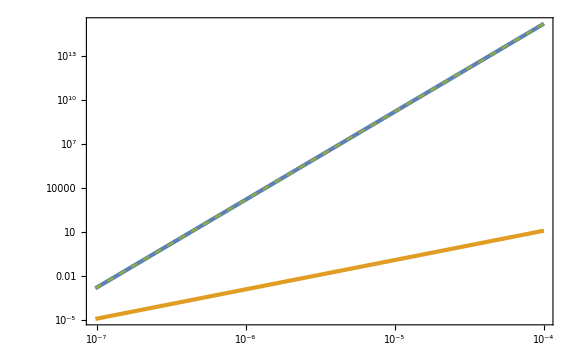

```mathematica
LogLogPlot[{Abs[(-((1+4 v[x]+v[x]^2) v'[x]^2)+2 v[x]^2 (1+v[x]) v''[x])/(4 v[x]^3)]/.{v[x]->vh[x],v'[x]->vh'[x],v''[x]->vh''[x]}/.{p->4,M->10^-2,v0->10^-14 10^-8},Abs[-((-1+p) p (1+v0) (x/M)^p)/x^2]/.{p->4,M->10^-2,v0->10^-14 10^-8},Abs[(p (x/M)^p (-p (x/M)^p+(-1+p) v0^2 (-1+(x/M)^p)-v0 (-1+p+(x/M)^p+2 p (x/M)^p)))/(v0 x^2)]/.{p->4,M->10^-2,v0->10^-14 10^-8}},{x,0,10^-4},PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],Dashed}]
```

```mathematica
LFPFhill=Collect[Simplify[Normal[Series[Simplify[LFPF/.{v[x]->vh[ϵ^(1/p) M],v'[x]->vh'[ϵ^(1/p) M],v''[x]->vh''[ϵ^(1/p) M]},{ϵ>0,p>0}],{ϵ,0,1}]]/.{ϵ->(x/M)^p},{p>0,x>0,M>0}],{F[x],F'[x],F''[x]},Simplify]
```

-M^-p (-1+p) p (1+v0) x^(-2+p) F[x]-2 M^-p p v0 x^(-1+p) F'[x]+(v0-2 M^-p v0 x^p) F''[x]

```mathematica
DSolve[(-vh'[x])/vh[x] F'[x]+vh[x]F''[x]==-Λn F[x]/.{p->2},F[x],x]
```

{{F[x]→[x]}}

```mathematica
DSolve[(-vh'[x])/vh[x] F'[x]+vh[x]F''[x]==-Λn F[x]/.{p->4},F[x],x]
```

$Aborted

```mathematica
F2[x_]=F[x]/.DSolve[LFPFhill==-Λn F[x]/.{p->2},F[x],x][[1]]//Simplify
```

C[1] LegendreP[1/2 (-1+(√(-4-3 v0+2 M^2 Λn))/(√v0)),(√2 x)/M]+C[2] LegendreQ[1/2 (-1+(√(-4-3 v0+2 M^2 Λn))/(√v0)),(√2 x)/M]

```mathematica
Normal[Series[HeunB[(2+2 v0-M^2 Λn)/(4 M^2 v0),(-2-5 v0+v0^2)/(2 M^4 v0^2),1/2,-2/M^2,2/M^4,x^2],{x,0,2}]]
```

1+(x^2 (2+2 v0-M^2 Λn))/(2 M^2 v0)

```mathematica
vh''[x]/vh[x]/.{p->2}/.{x->0}//Simplify
```

-4/M^2

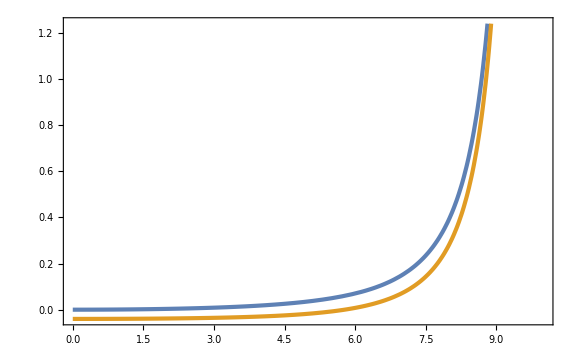

```mathematica
Plot[{1/2(vh'[x]/vh[x])^2/.{p->2,M->10},vh''[x]/vh[x]/.{p->2,M->10}},{x,0,10}]
```

```mathematica
(x/.Solve[vh''[x]/vh[x]==1/.{p->2},x][[2]]//Simplify)/.{M->10}//N
```

8.77988

```mathematica
Normal[Series[x/.Solve[vh''[x]/vh[x]==1/.{p->2},x][[2]],{M,∞,0}]]/.{M->10}//N
```

8.58579

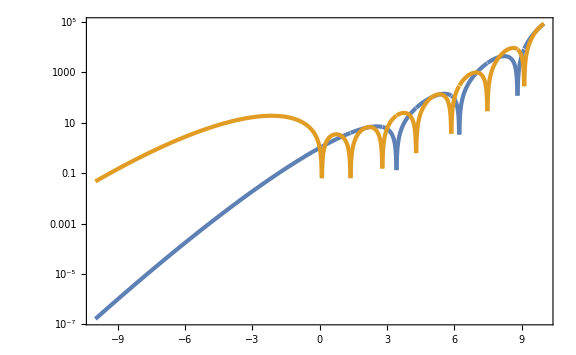

```mathematica
LogPlot[{HermiteH[a,Sqrt[2]]//Abs,HermiteH[a,-Sqrt[2]]//Abs},{a,-10,10}]
```

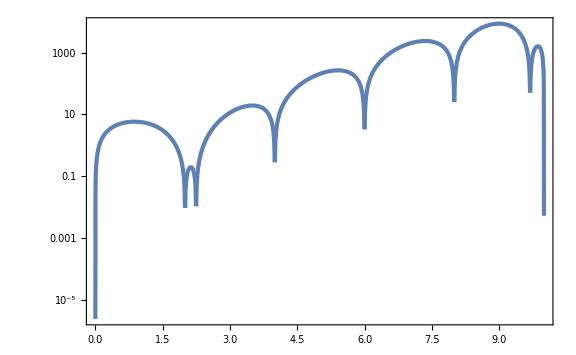

```mathematica
LogPlot[{HermiteH[a,Sqrt[2]]-HermiteH[a,-Sqrt[2]]//Abs},{a,0,10}]
```

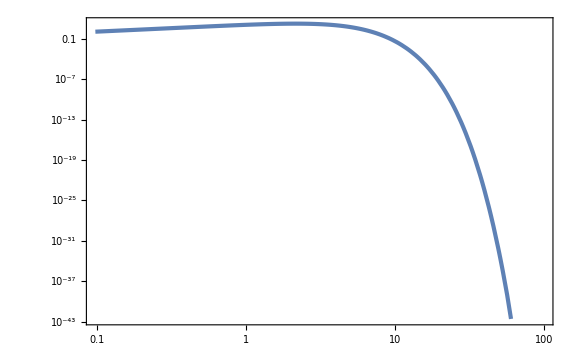

```mathematica
LogLogPlot[{HermiteH[-a,Sqrt[2]]-HermiteH[-a,-Sqrt[2]]//Abs},{a,0,10^2}]
```

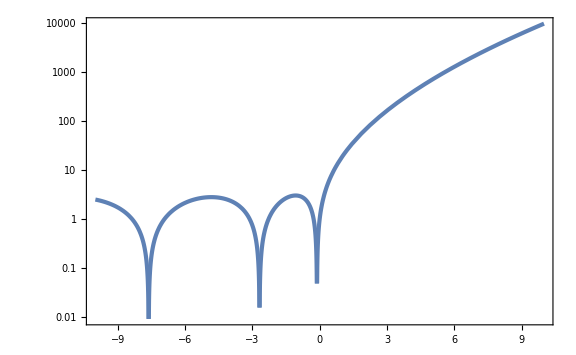

```mathematica
LogPlot[Hypergeometric1F1[a,1/2,2]//Abs,{a,-10,10}]
```

```mathematica
HermiteH[a,Sqrt[2]]//FunctionExpand
```

HermiteH[a,√2]

```mathematica
Hypergeometric1F1[a,1/2,2]//FullSimplify
```

Hypergeometric1F1[a,1/2,2]

```mathematica
HermiteH[2,x]
```

-2+4 x^2

```mathematica
Hypergeometric1F1[-1,1/2,x^2]
```

1-2 x^2

```mathematica
DSolve[LFPFhill==-Λn F[x]/.{p->4}//Simplify,F[x],x]//Simplify
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity^(1/2 (-3/2+√(9/4-(12+Times[«2»])/(2 v0)))) encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity^(1/2 (-5/2-√(9/4-1/2 Power[«2»] Plus[«2»]))) encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity^(1/2 (-3/2+√(9/4-(12+Times[«2»])/(2 v0)))) encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{F[x]→C[1] HeunG[-1,-(M^2 Λn)/(4 √2 v0),3/4-1/4 √3 √(-5-8/v0),3/4+1/4 √3 √(-5-8/v0),1/2,1,-(√2 x^2)/M^2]+2^(1/4) √(-x^2/M^2) C[2] HeunG[-1,-(M^2 Λn)/(4 √2 v0),5/4+1/4 √3 √(-5-8/v0),5/4-1/4 √3 √(-5-8/v0),3/2,1,-(√2 x^2)/M^2]}}

```mathematica
Normal[Series[HeunG[-1,-(M^2 Λn)/(4 √2 v0),3/4-1/4 √3 √(-5-8/v0),3/4+1/4 √3 √(-5-8/v0),1/2,1,-(√2 x^2)/M^2],{x,0,2}]]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity^(-3/4+1/4 √3 √(-5-8/v0)) encountered.

1-(x^2 Λn)/(2 v0)

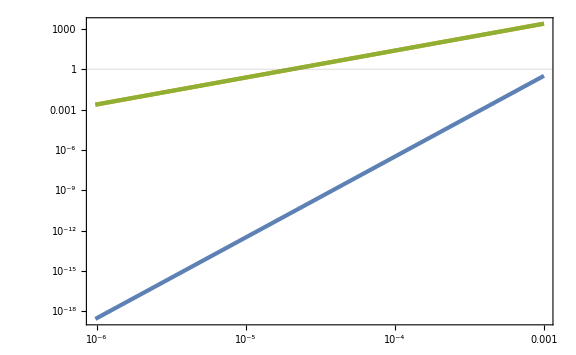

```mathematica
LogLogPlot[{1/2(vh'[x]/vh[x])^2/.{p->4,M->10^-2},Abs[vh''[x]/vh[x]/.{p->4,M->10^-2}],Abs[vh''[x]/v0/.{p->4,M->10^-2}]},{x,0,10^-3},GridLines->{None,{1}}]
```

```mathematica
Normal[Series[vh''[x]/vh[x]/.{p->4},{x,0,2}]]
```

-(24 x^2)/M^4

```mathematica
xf=x/.Solve[Normal[Series[Simplify[vh''[x]/v0==-1/.{p->4}],{x,0,2}]],x][[2]]
```

M^2/(2 √6)

```mathematica
Normal[Series[HeunB[-Λn/(4 v0),-(3 (1+v0))/(M^4 v0),1/2,0,-4/M^4,x^2],{x,0,2}]]
```

1-(x^2 Λn)/(2 v0)

```mathematica
Normal[Series[HeunB[-Λn/(4 v0),-(3+5 v0)/(M^4 v0),3/2,0,-4/M^4,x^2],{x,0,2}]]
```

1-(x^2 Λn)/(6 v0)

```mathematica
Solve[Normal[Series[HeunB[-Λn/(4 v0),-(3 (1+v0))/(M^4 v0),1/2,0,-4/M^4,x^2],{x,0,2}]]==0/.{x->xf},Λn]
```

{{Λn→(48 v0)/M^4}}

```mathematica
Normal[Series[1/(12 π^2)vh[x]^3/vh'[x]^2/.{p->4,x->xf/(2/3 NN)^(1/2)},{M,0,-4}]]
```

(16 NN^3 v0)/(3 M^4 π^2)

```mathematica
v0sol=Solve[Normal[Series[1/(12 π^2)vh[x]^3/vh'[x]^2/.{p->4,x->xf/(2/3 NN)^(1/2)},{M,0,-4}]]==2 10^-9,v0][[1]]
```

{v0→(3 M^4 π^2)/(8000000000 NN^3)}

```mathematica
v0/M^4/.v0sol/.{NN->60}//N
```

1.71347×10^-14

```mathematica
λ Mp^4/.Solve[(p^(2/(p-2))(p-2)^((2(p-1))/(p-2)))/(2^((2(p-3))/(p-2))3 π^2)λ Mp^(2(p-2))(M/Mp)^((2p(p-3))/(p-2))NN^((2(p-1))/(p-2))==2 10^-9/.{p->4},λ][[1]]/.{M->10^-2 Mp,NN->60}//N
```

1.71347×10^-6

```mathematica
(v0 π^2)/(2xf)^2
```

(6 π^2 v0)/M^4

```mathematica
6 π^2//N
```

59.2176

```mathematica
1/((p-2)/(p-1)NN)^(1/(p-2))/.{p->4,NN->60}
```

1/(2 √10)

### chaotic

```mathematica
$Assumptions={m>0,x>0,vv>0};
```

```mathematica
v[x_]=1/2 m^2 x^2;
```

```mathematica
w[x_]=E^(1/v[x])/v[x];
LFPF=Collect[w[x]^(1/2)((-v'[x])/v[x] D[(w[x]^(-1/2)F[x]), x]+v[x]D[D[(w[x]^(-1/2)F[x]), x], x])//Simplify,{F[x],F'[x],F''[x]},Simplify]
```

(-2/(m^2 x^4)-3/x^2) F[x]+m^2 x F'[x]+1/2 m^2 x^2 F''[x]

```mathematica
DSolve[LFPF==-Λn F[x],F[x],x]
```

{{F[x]→[x]}}

```mathematica
Forig[x_]=F[x]/.DSolve[(-v'[x])/v[x] F'[x]+v[x]F''[x]==-Λn F[x],F[x],x][[1]]/.{x->Sqrt[2 vt[x]/m^2]}//Simplify//Expand
```

C[2] Hypergeometric1F1[(-m+√(m^2-8 Λn))/(4 m),1+(√(m^2-8 Λn))/(2 m),-1/vt[x]] vt[x]^((m-√(m^2-8 Λn))/(4 m))+C[1] Hypergeometric1F1[-(m+√(m^2-8 Λn))/(4 m),1-(√(m^2-8 Λn))/(2 m),-1/vt[x]] vt[x]^((m-√(m^2-8 Λn))/(4 m)+(√(m^2-8 Λn))/(2 m))

```mathematica
F1[vv_]=Sqrt[E^(1/vv)/vv] vv^((1-νn)/4)Hypergeometric1F1[(νn-1)/4,1+νn/2,-1/vv]//Simplify
F2[vv_]=Sqrt[E^(1/vv)/vv] vv^((1+νn)/4)Hypergeometric1F1[(-νn-1)/4,1-νn/2,-1/vv]//Simplify
```

ⅇ^(1/2/vv) vv^(-1/4-νn/4) Hypergeometric1F1[1/4 (-1+νn),(2+νn)/2,-1/vv]

ⅇ^(1/2/vv) vv^(1/4 (-1+νn)) Hypergeometric1F1[1/4 (-1-νn),1-νn/2,-1/vv]

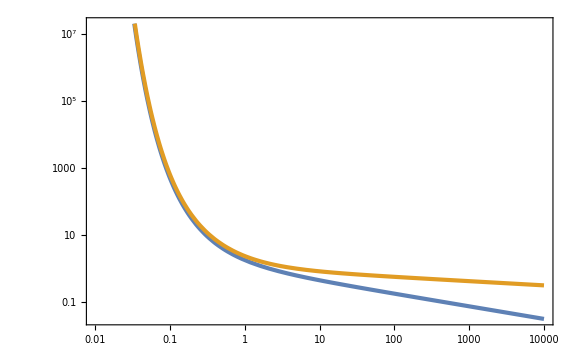

```mathematica
LogLogPlot[{F1[vv]/.{νn->1/2},F2[vv]/.{νn->1/2}},{vv,10^-2,10^4}]
```

```mathematica
Normal[Series[F1[vv]/.{νn->1/2},{v,∞,0}]]//Simplify
```

(ⅇ^(1/2/vv) Hypergeometric1F1[-1/8,5/4,-1/vv])/vv^(3/8)

```mathematica
Normal[Series[F2[vv]/.{νn->1/2},{v,∞,0}]]//Simplify
```

(ⅇ^(1/2/vv) Hypergeometric1F1[-3/8,3/4,-1/vv])/vv^(1/8)

```mathematica
vf=v[Sqrt[2]]
```

m^2

```mathematica
Fsol[vv_]=F1[vv]-F1[vf]/F2[vf] F2[vv]//Simplify
```

ⅇ^(1/2/vv) vv^(-1/4-νn/4) (-(m^-νn vv^(νn/2) Hypergeometric1F1[1/4 (-1-νn),1-νn/2,-1/vv] Hypergeometric1F1[1/4 (-1+νn),(2+νn)/2,-1/m^2])/Hypergeometric1F1[1/4 (-1-νn),1-νn/2,-1/m^2]+Hypergeometric1F1[1/4 (-1+νn),(2+νn)/2,-1/vv])

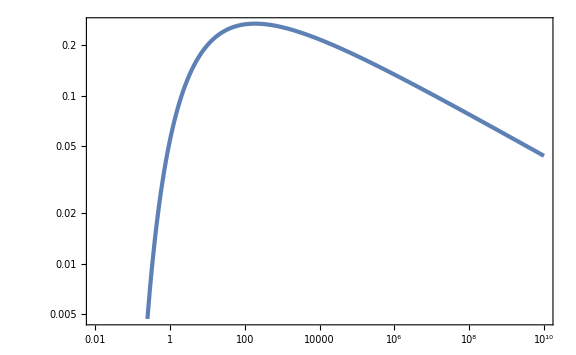

```mathematica
LogLogPlot[Abs[Fsol[vv]/.{m->10^-1,νn->1/2}],{vv,vf/.{m->10^-1},10^10},WorkingPrecision->30]
```